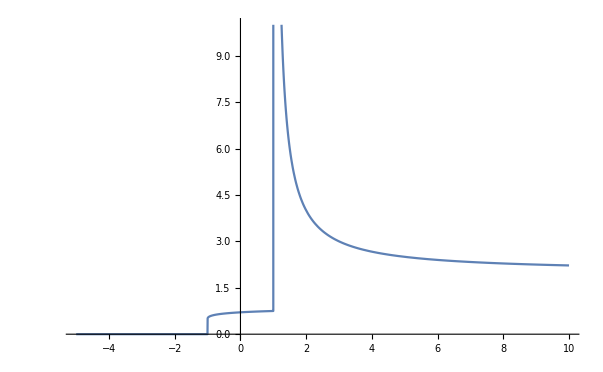

```mathematica
m = 1;
a = 1;
b = 0;
B0 = -1;
kp[E_] := Sqrt[ 2m (E+ m(a^2+b^2) + Sqrt[(E+m(a^2+b^2))^2 + B0^2 - E^2])]
km[E_] := Sqrt[ 2m (E+ m(a^2+b^2) - Sqrt[(E+m(a^2+b^2))^2 + B0^2 - E^2])]
DOS[E_]:=  ( (1/m + (a^2 + b^2)/Sqrt[(a^2+b^2)kp[E]^2 + B0^2])^(-1)  θ[kp[E]])+ ( (1/m - (a^2 + b^2)/Sqrt[(a^2+b^2)km[E]^2 + B0^2])^(-1) θ[km[E]])
Plot[DOS[E],{E,-5,10}, PlotRange->{0,10}]
```

```mathematica
θ[x_] := 1 /;(Im[x] == 0&& x≥ 0)
θ[x_]:= 0;
θ[12+ⅈ]
```

0

```mathematica
(*Clear[θ]*)
```